```mathematica
Clear[unique];
unique[L_,n_]:=(
Count[Map[correct,combinations[L,Length[L]-n]],True]==1)
```

```mathematica
correct[L_]:=If[valid[L],ToExpression[StringJoin[L]]===True,False]
```

```mathematica
valid[L_]:=Module[{},
loc=Flatten[Position[L,x_/;MemberQ[nums,x]]];
If[loc=={},Print["error"]];
Max[Rest[loc-RotateRight[loc]]]<3&&MemberQ[loc,1]&&MemberQ[loc,Length[L]]]
```

```mathematica
combinations[L_,k_]:={L}/;Length[L]==k
combinations[L_,0]:={{}}
combinations[L_,k_]:=Sort[Join[combinations[Rest[L],k],Map[Prepend[#,First[L]]&,combinations[Rest[L],k-1]]]]
```

```mathematica
nums={"1","2","3","4","5","6","7","8","9"};
```

```mathematica
strings={"1","2","3","4","5","6","7","8","9","+","-","×","÷"};
```

```mathematica
soln[L_,m_]:=Module[{a,b,n=Length[L]},
a=
Map[List,combinations[Range[Length[L]],m],{2}];
b=Flatten[Select[Select[a,valid[Delete[L,#]]&],ToExpression[StringJoin[Delete[L,#]]]&]]]
```

```mathematica
r[n_]:=Module[{},
temp={};
While[Not[.6(n-1)<Count[temp,x_/;MemberQ[nums,x]]<.8(n-1)]||Not[valid[temp]],
temp=Join[{nums[[RandomInteger[{1,9}]]]},Table[strings[[RandomInteger[{1,13}]]],{n-2}],{nums[[RandomInteger[{1,9}]]]}];
eqloc=RandomInteger[{Floor[n/3],Ceiling[2n/3]}];temp[[eqloc]]="==";];
temp
]
```

```mathematica
pic[L_]:=Module[{n=Length[L]},
Style[Show[Graphics[{
Line[{{0,0},{n,0},{n,1},{0,1},{0,0}}],
Table[Line[{{i,0},{i,1}}],{i,1,n-1}],
Table[If[L[[i]]=="==",Text[Style["=",FontFamily->"Courier",FontSize->16],{i-1/2,1/2}],Text[Style[L[[i]],FontFamily->"Courier",FontSize->16],{i-1/2,1/2}]],{i,1,n}]
}],ImageSize->20n,PlotRange->{{-.02,n+.02},{-.02,1.02}}],Antialiasing->False]]
```

```mathematica
pic[L_,omit_]:=Module[{n=Length[L]},
Style[Show[Graphics[{
Table[If[L[[i]]=="==",Text[Style["=",FontFamily->"Courier",FontSize->16],{i-1/2,1/2}],Text[Style[L[[i]],FontFamily->"Courier",FontSize->16],{i-1/2,1/2}]],{i,1,n}],Brown,
Map[Rectangle[{#-1,0},{#,1}]&,omit],Black,Line[{{0,0},{n,0},{n,1},{0,1},{0,0}}],
Table[Line[{{i,0},{i,1}}],{i,1,n-1}]
}],ImageSize->20n,PlotRange->{{-.02,n+.02},{-.02,1.02}}],Antialiasing->False]
]
```

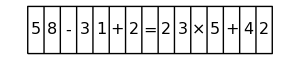

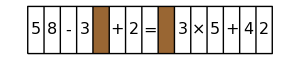

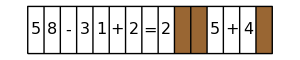

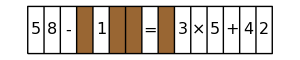

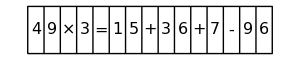

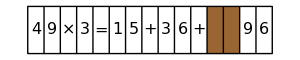

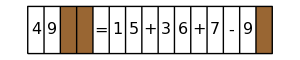

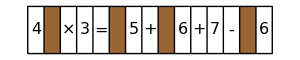

$Aborted

```mathematica
For[i=1,i>0,i++,
q=r[15];
While[Not[unique[q,2]]||Not[unique[q,3]]||Not[unique[q,4]],q=r[15]];
q2=soln[q,2];q3=soln[q,3];q4=soln[q,4];If[Length[Intersection[q2,q3]]+Length[Intersection[q2,q4]]+Length[Intersection[q3,q4]]<2&&Min[Join[q2,q3,q4]]<eqloc<Max[Join[q2,q3,q4]],Print[pic[q]];Print[pic[q,q2]];Print[pic[q,q3]];Print[pic[q,q4]];Print[]]]
```

```mathematica
For[i=1,i>0,i++,
q=r[13];
While[Not[unique[q,2]]||Not[unique[q,3]],q=r[13]];
q2=soln[q,2];q3=soln[q,3];If[Intersection[q2,q3]=={}&&Min[Join[q2,q3]]<eqloc<Max[Join[q2,q3]],Print[pic[q]];Print[pic[q,q2]];Print[pic[q,q3]];Print[]]]
```